# False Random Trend Lines

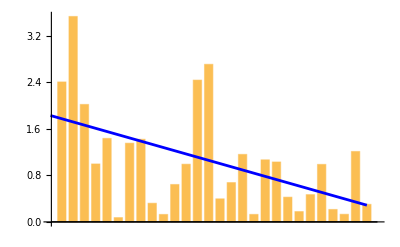
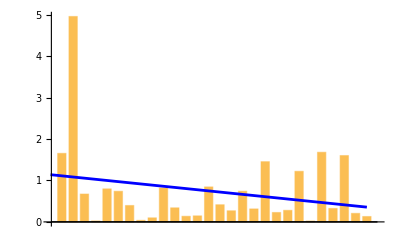
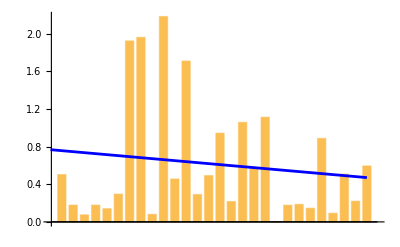
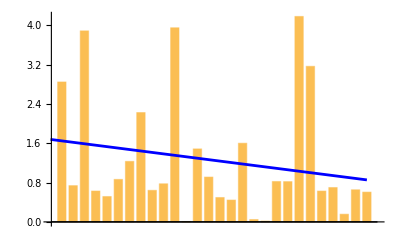
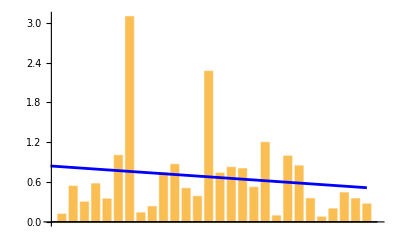
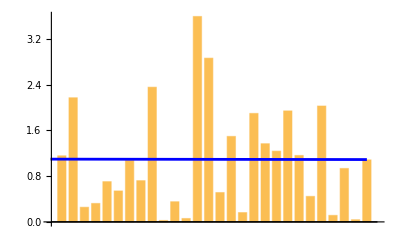
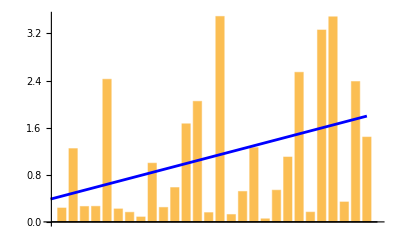
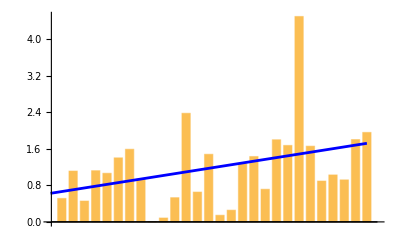

```mathematica
Table[data = RandomVariate[ExponentialDistribution[1],{28}];
lm = LinearModelFit[data,x,x];
Show[BarChart[data], Plot[lm[x],{x,0,28},PlotStyle->Blue,Frame->True]],{12}]
```

## Normal distribution

```mathematica
ta=Table[data = RandomVariate[ExponentialDistribution[1],{28}]; lm=LinearModelFit[data,x,x]; lm[[1]][[2]][[2]],{10^5}];
```

```mathematica
{Mean[ta], StandardDeviation[ta]}
```

{0.0000698493,0.0233824}

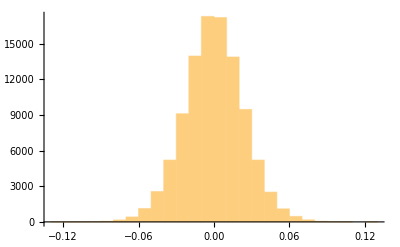

```mathematica
Histogram[ta]
```

## Logistic Distribution

Submitted by someone who did parallel computation with tabulation. I did not know this was a thing.

```mathematica
?ParallelTable
```

```mathematica
?Block
```

```mathematica
ta = ParallelTable[Block[{data,lm}, data=RandomVariate[ExponentialDistribution[1],{28}]; lm=LinearModelFit[data,x,x];lm["BestFitParameters"][[2]]],{100000}];
```

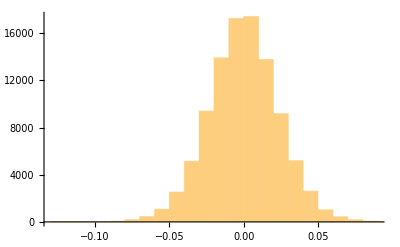

```mathematica
Histogram[ta]
```

```mathematica
FindDistribution[ta]
```

LogisticDistribution[-0.0000683879,0.0132023]

```mathematica
{Mean[ta],StandardDeviation[ta]}
```

{-0.0000634032,0.0234394}